## Аппроксимация Паде Баталов С.А.

```mathematica
ClearAll["Global`*"]
```

### Условие задачи

```mathematica
Eq0 = y^4 - ϵ * y - 2 * y^2 - 8 == 0
```

-8-2 y^2+y^4-y ϵ==0

### Решение при

```mathematica
Y0 = y[0] + ϵ * y[1] + ϵ^2 * y[2]
```

y[0]+ϵ y[1]+ϵ^2 y[2]

```mathematica
SolY0 = Solve[Table[Coefficient[Series[Eq0[[1]] /. {y -> Y0}, {ϵ, 0, 2}], ϵ, i] == 0, {i, 0, 2}], {y[0], y[1], y[2]}];
Sol0 = (y -> Y0) /. SolY0
```

{y→-2+ϵ/12+(5 ϵ^2)/1728,y→2+ϵ/12-(5 ϵ^2)/1728,y→-ⅈ √2-ϵ/12-(ⅈ ϵ^2)/(864 √2),y→ⅈ √2-ϵ/12+(ⅈ ϵ^2)/(864 √2)}

### Решение при

```mathematica
EqInf = Collect[MultiplySides[Eq0 /. {ϵ -> 1 / τ}, τ > 0], τ]
```

-y+(-8-2 y^2+y^4) τ==0

```mathematica
YInf = τ^k * x[1];
Collect[Expand[EqInf /. {y -> YInf}], {τ, τ^(_)}]
```

-8 τ-τ^k x[1]-2 τ^(1+2 k) x[1]^2+τ^(1+4 k) x[1]^4==0

```mathematica
SolInf = {y -> -8 / ϵ, y -> ϵ ^ (1 / 3)}
```

{y→-8/ϵ,y→ϵ^(1/3)}

### Переход к новому параметру

```mathematica
Sol0Mu = Sol0 /. {ϵ -> μ^3}
```

{y→-2+μ^3/12+(5 μ^6)/1728,y→2+μ^3/12-(5 μ^6)/1728,y→-ⅈ √2-μ^3/12-(ⅈ μ^6)/(864 √2),y→ⅈ √2-μ^3/12+(ⅈ μ^6)/(864 √2)}

```mathematica
SolInfMu = Simplify[SolInf /. {ϵ -> μ^3}, μ > 0]
```

{y→-8/μ^3,y→μ}

### Сращивание вещественных решений

#### Первый корень

```mathematica
F1 = Sum[c[i] * μ^i, {i, 0, 3}] / Sum[d[i] * μ^i, {i, 0, 6}] /. {c[0] -> 1}
```

(1+μ c[1]+μ^2 c[2]+μ^3 c[3])/(d[0]+μ d[1]+μ^2 d[2]+μ^3 d[3]+μ^4 d[4]+μ^5 d[5]+μ^6 d[6])

```mathematica
SolF1 = Solve[Union[Thread[CoefficientList[Numerator[F1] - Denominator[F1] * Sol0Mu[[1, 2]], μ] == 0][[1;;9]], 
	{Coefficient[Series[Simplify[F1], {μ, Infinity, 3}], μ, -3] == -8}], 
	Union[Table[c[i], {i, 1, 3}], Table[d[i], {i, 0, 6}]]][[1]]
```

{c[1]→0,c[2]→0,c[3]→11/720,d[0]→-1/2,d[1]→0,d[2]→0,d[3]→-41/1440,d[4]→0,d[5]→0,d[6]→-11/5760}

```mathematica
y1 = Simplify[(F1 /. SolF1) /. {μ -> ϵ^(1/3)}]
```

-(8 (720+11 ϵ))/(2880+164 ϵ+11 ϵ^2)

#### Второй корень

```mathematica
F2 = Sum[a[i] * μ^i, {i, 0, 5}] / Sum[b[i] * μ^i, {i, 0, 4}] /. {a[0] -> 1}
```

(1+μ a[1]+μ^2 a[2]+μ^3 a[3]+μ^4 a[4]+μ^5 a[5])/(b[0]+μ b[1]+μ^2 b[2]+μ^3 b[3]+μ^4 b[4])

```mathematica
SolF2 = Solve[Union[Thread[CoefficientList[Numerator[F2] - Denominator[F2] * Sol0Mu[[2, 2]], μ] == 0][[1;;8]], 
	Thread[CoefficientList[Series[Simplify[F2], {μ, Infinity, 0}], μ] == {0, 1}]], Union[Table[a[i], {i, 1, 5}], Table[b[i], {i, 0, 4}]]][[1]]
```

{a[1]→5/22,a[2]→25/264,a[3]→11/144,a[4]→5/288,a[5]→25/6336,b[0]→1/2,b[1]→5/44,b[2]→25/528,b[3]→5/288,b[4]→25/6336}

```mathematica
y2 = Simplify[(F2 /. SolF2) /. {μ -> ϵ^(1/3)}]
```

(6336+1440 ϵ^(1/3)+600 ϵ^(2/3)+484 ϵ+110 ϵ^(4/3)+25 ϵ^(5/3))/(3168+720 ϵ^(1/3)+300 ϵ^(2/3)+110 ϵ+25 ϵ^(4/3))

### Построение решений

#### Первый корень

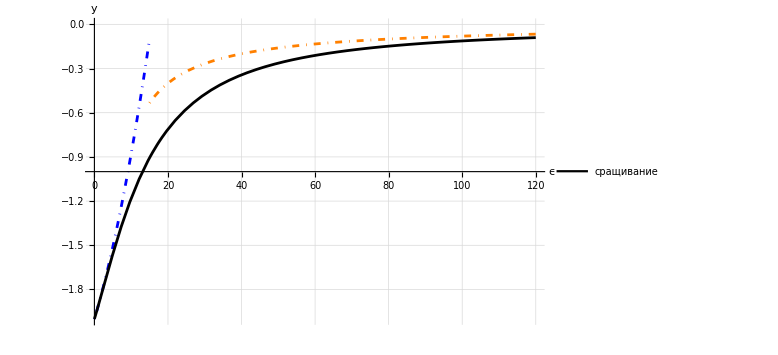

```mathematica
Show[{Plot[Sol0[[1, 2]], {ϵ, 0, 15}, PlotStyle -> {Blue, DotDashed}, PlotLegends -> LineLegend[{Blue}, {""}]],
	Plot[SolInf[[1, 2]], {ϵ, 15, 120}, PlotStyle -> {Orange, DotDashed}, PlotLegends -> LineLegend[{Orange}, {""}]], 
	Plot[y1, {ϵ, 0, 120}, PlotStyle -> Black, PlotLegends -> LineLegend[{Black}, {"сращивание"}]]},
	AxesLabel -> {ϵ, y}, GridLines -> Automatic, PlotRange -> {Automatic, {-2, 0}}, AxesOrigin -> {0, -1}, ImageSize -> Large]
```

#### Второй корень

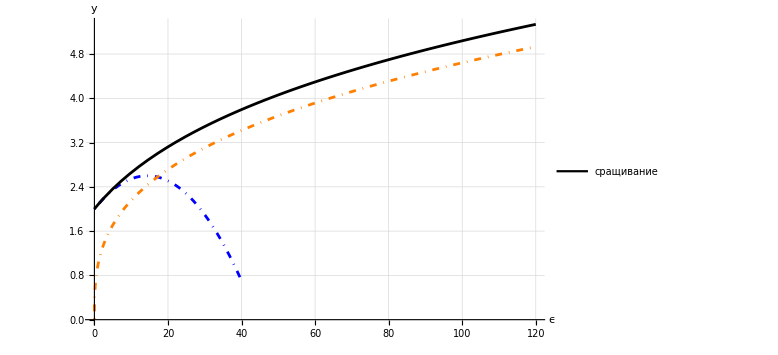

```mathematica
Show[{Plot[Sol0[[2, 2]], {ϵ, 0, 40}, PlotStyle -> {Blue, DotDashed}, PlotLegends -> LineLegend[{Blue}, {""}]],
	Plot[SolInf[[2, 2]], {ϵ, 0, 120}, PlotStyle -> {Orange, DotDashed}, PlotLegends -> LineLegend[{Orange}, {""}]], 
	Plot[y2, {ϵ, 0, 120}, PlotStyle -> Black, PlotLegends -> LineLegend[{Black}, {"сращивание"}]]}, AxesLabel -> {ϵ, y}, 
	GridLines -> Automatic, PlotRange -> {Automatic, Automatic}, AxesOrigin -> {0, 0}, ImageSize -> Large]
```